```mathematica
(* some auxiliary symbols *)
Q[k_]:={{1,0,0},{0,1,0},{0,0,(-1)^k}}
c[k_]:=(-1)^k*h*{0,0,1}

xEigen[k_]:=({x,y,z}-c[k]).(Q[k][[All,1]])
yEigen[k_]:=({x,y,z}-c[k]).(Q[k][[All,2]])
zEigen[k_]:=({x,y,z}-c[k]).(Q[k][[All,3]])

X[k_,l_]:=xEigen[k]+(-1)^l*w
Y[k_,l_]:=yEigen[k]+(-1)^l*d
Z[k_]:=zEigen[k]

R[k_,l_,m_]:=Sqrt[X[k,l]^2+Y[k,m]^2+Z[k]^2]
```

```mathematica
(* potential *)
V=Sum[
(-1)^(k+l+m)*(
-Z[k]*ArcTan[X[k,l]*Y[k,m]/Z[k]/R[k,l,m]]+X[k,l]*Log[Y[k,m]+R[k,l,m]]+Y[k,m]*Log[X[k,l]+R[k,l,m]]
),
{k,1,2},{l,1,2},{m,1,2}];
```

### x

```mathematica
DxV=Sum[
(-1)^(k+l+m)*(
-(Y[k,m]/R[k,l,m]-X[k,l]^2*Y[k,m]/R[k,l,m]^3)/(1+(X[k,l]*Y[k,m]/Z[k]/R[k,l,m])^2)+Log[Y[k,m]+R[k,l,m]]+X[k,l]^2/(R[k,l,m]*(Y[k,m]+R[k,l,m]))+Y[k,m]*(1+X[k,l]/R[k,l,m])/(X[k,l]+R[k,l,m])
),
{k,1,2},{l,1,2},{m,1,2}];
```

```mathematica
D[V,x]-DxV//Simplify
```

0

Simplify expression “manually”:
Part 1:

```mathematica
Sum[
(-1)^(k+l+m)*(
-(Y[k,m]/R[k,l,m]-X[k,l]^2*Y[k,m]/R[k,l,m]^3)/(1+(X[k,l]*Y[k,m]/Z[k]/R[k,l,m])^2)
),
{k,1,2},{l,1,2},{m,1,2}]
```

-(((-w+x)^2 (-d+y))/(((-w+x)^2+(-d+y)^2+(-h-z)^2)^(3/2))-(-d+y)/(√((-w+x)^2+(-d+y)^2+(-h-z)^2)))/(1+((-w+x)^2 (-d+y)^2)/(((-w+x)^2+(-d+y)^2+(-h-z)^2) (-h-z)^2))+(((w+x)^2 (-d+y))/(((w+x)^2+(-d+y)^2+(-h-z)^2)^(3/2))-(-d+y)/(√((w+x)^2+(-d+y)^2+(-h-z)^2)))/(1+((w+x)^2 (-d+y)^2)/(((w+x)^2+(-d+y)^2+(-h-z)^2) (-h-z)^2))+(((-w+x)^2 (d+y))/(((-w+x)^2+(d+y)^2+(-h-z)^2)^(3/2))-(d+y)/(√((-w+x)^2+(d+y)^2+(-h-z)^2)))/(1+((-w+x)^2 (d+y)^2)/(((-w+x)^2+(d+y)^2+(-h-z)^2) (-h-z)^2))-(((w+x)^2 (d+y))/(((w+x)^2+(d+y)^2+(-h-z)^2)^(3/2))-(d+y)/(√((w+x)^2+(d+y)^2+(-h-z)^2)))/(1+((w+x)^2 (d+y)^2)/(((w+x)^2+(d+y)^2+(-h-z)^2) (-h-z)^2))+(((-w+x)^2 (-d+y))/(((-w+x)^2+(-d+y)^2+(-h+z)^2)^(3/2))-(-d+y)/(√((-w+x)^2+(-d+y)^2+(-h+z)^2)))/(1+((-w+x)^2 (-d+y)^2)/((-h+z)^2 ((-w+x)^2+(-d+y)^2+(-h+z)^2)))-(((w+x)^2 (-d+y))/(((w+x)^2+(-d+y)^2+(-h+z)^2)^(3/2))-(-d+y)/(√((w+x)^2+(-d+y)^2+(-h+z)^2)))/(1+((w+x)^2 (-d+y)^2)/((-h+z)^2 ((w+x)^2+(-d+y)^2+(-h+z)^2)))-(((-w+x)^2 (d+y))/(((-w+x)^2+(d+y)^2+(-h+z)^2)^(3/2))-(d+y)/(√((-w+x)^2+(d+y)^2+(-h+z)^2)))/(1+((-w+x)^2 (d+y)^2)/((-h+z)^2 ((-w+x)^2+(d+y)^2+(-h+z)^2)))+(((w+x)^2 (d+y))/(((w+x)^2+(d+y)^2+(-h+z)^2)^(3/2))-(d+y)/(√((w+x)^2+(d+y)^2+(-h+z)^2)))/(1+((w+x)^2 (d+y)^2)/((-h+z)^2 ((w+x)^2+(d+y)^2+(-h+z)^2)))

Part 1.1:

```mathematica
-(((-w+x)^2 (-d+y))/(((-w+x)^2+(-d+y)^2+(-h-z)^2)^(3/2))-(-d+y)/(√((-w+x)^2+(-d+y)^2+(-h-z)^2)))/(1+((-w+x)^2 (-d+y)^2)/(((-w+x)^2+(-d+y)^2+(-h-z)^2) (-h-z)^2))+(((w+x)^2 (-d+y))/(((w+x)^2+(-d+y)^2+(-h-z)^2)^(3/2))-(-d+y)/(√((w+x)^2+(-d+y)^2+(-h-z)^2)))/(1+((w+x)^2 (-d+y)^2)/(((w+x)^2+(-d+y)^2+(-h-z)^2) (-h-z)^2))+(((-w+x)^2 (d+y))/(((-w+x)^2+(d+y)^2+(-h-z)^2)^(3/2))-(d+y)/(√((-w+x)^2+(d+y)^2+(-h-z)^2)))/(1+((-w+x)^2 (d+y)^2)/(((-w+x)^2+(d+y)^2+(-h-z)^2) (-h-z)^2))-(((w+x)^2 (d+y))/(((w+x)^2+(d+y)^2+(-h-z)^2)^(3/2))-(d+y)/(√((w+x)^2+(d+y)^2+(-h-z)^2)))/(1+((w+x)^2 (d+y)^2)/(((w+x)^2+(d+y)^2+(-h-z)^2) (-h-z)^2))//Simplify
```

(h+z)^2 ((-d+y)/((h^2+w^2-2 w x+x^2+2 h z+z^2) √(d^2+h^2+w^2-2 w x+x^2-2 d y+y^2+2 h z+z^2))+(d-y)/((h^2+w^2+2 w x+x^2+2 h z+z^2) √((w+x)^2+(d-y)^2+(h+z)^2))-(d+y)/((h^2+w^2-2 w x+x^2+2 h z+z^2) √((w-x)^2+(d+y)^2+(h+z)^2))+(d+y)/((h^2+w^2+2 w x+x^2+2 h z+z^2) √((w+x)^2+(d+y)^2+(h+z)^2)))

Part 1.2:

```mathematica
+(((-w+x)^2 (-d+y))/(((-w+x)^2+(-d+y)^2+(-h+z)^2)^(3/2))-(-d+y)/(√((-w+x)^2+(-d+y)^2+(-h+z)^2)))/(1+((-w+x)^2 (-d+y)^2)/((-h+z)^2 ((-w+x)^2+(-d+y)^2+(-h+z)^2)))-(((w+x)^2 (-d+y))/(((w+x)^2+(-d+y)^2+(-h+z)^2)^(3/2))-(-d+y)/(√((w+x)^2+(-d+y)^2+(-h+z)^2)))/(1+((w+x)^2 (-d+y)^2)/((-h+z)^2 ((w+x)^2+(-d+y)^2+(-h+z)^2)))-(((-w+x)^2 (d+y))/(((-w+x)^2+(d+y)^2+(-h+z)^2)^(3/2))-(d+y)/(√((-w+x)^2+(d+y)^2+(-h+z)^2)))/(1+((-w+x)^2 (d+y)^2)/((-h+z)^2 ((-w+x)^2+(d+y)^2+(-h+z)^2)))+(((w+x)^2 (d+y))/(((w+x)^2+(d+y)^2+(-h+z)^2)^(3/2))-(d+y)/(√((w+x)^2+(d+y)^2+(-h+z)^2)))/(1+((w+x)^2 (d+y)^2)/((-h+z)^2 ((w+x)^2+(d+y)^2+(-h+z)^2)))//Simplify
```

(h-z)^2 ((d-y)/(√((w-x)^2+(d-y)^2+(h-z)^2) (h^2+w^2-2 w x+x^2-2 h z+z^2))+(d+y)/(√((w-x)^2+(d+y)^2+(h-z)^2) (h^2+w^2-2 w x+x^2-2 h z+z^2))+(-d+y)/(√((w+x)^2+(d-y)^2+(h-z)^2) (h^2+w^2+2 w x+x^2-2 h z+z^2))-(d+y)/(√((w+x)^2+(d+y)^2+(h-z)^2) (h^2+w^2+2 w x+x^2-2 h z+z^2)))

Part 2:

```mathematica
Sum[
(-1)^(k+l+m)*(Log[Y[k,m]+R[k,l,m]]),
{k,1,2},{l,1,2},{m,1,2}]//Simplify
```

Log[-d+y+√((w-x)^2+(d-y)^2+(h-z)^2)]-Log[-d+y+√((w+x)^2+(d-y)^2+(h-z)^2)]-Log[d+y+√((w-x)^2+(d+y)^2+(h-z)^2)]+Log[d+y+√((w+x)^2+(d+y)^2+(h-z)^2)]-Log[-d+y+√((w-x)^2+(d-y)^2+(h+z)^2)]+Log[-d+y+√((w+x)^2+(d-y)^2+(h+z)^2)]+Log[d+y+√((w-x)^2+(d+y)^2+(h+z)^2)]-Log[d+y+√((w+x)^2+(d+y)^2+(h+z)^2)]

Part 3 (simplification not working):

```mathematica
Sum[
(-1)^(k+l+m)*(X[k,l]^2/(R[k,l,m]*(Y[k,m]+R[k,l,m]))
),
{k,1,2},{l,1,2},{m,1,2}]
```

-(-w+x)^2/((-d+y+√((-w+x)^2+(-d+y)^2+(-h-z)^2)) √((-w+x)^2+(-d+y)^2+(-h-z)^2))+(w+x)^2/((-d+y+√((w+x)^2+(-d+y)^2+(-h-z)^2)) √((w+x)^2+(-d+y)^2+(-h-z)^2))+(-w+x)^2/((d+y+√((-w+x)^2+(d+y)^2+(-h-z)^2)) √((-w+x)^2+(d+y)^2+(-h-z)^2))-(w+x)^2/((d+y+√((w+x)^2+(d+y)^2+(-h-z)^2)) √((w+x)^2+(d+y)^2+(-h-z)^2))+(-w+x)^2/(√((-w+x)^2+(-d+y)^2+(-h+z)^2) (-d+y+√((-w+x)^2+(-d+y)^2+(-h+z)^2)))-(w+x)^2/(√((w+x)^2+(-d+y)^2+(-h+z)^2) (-d+y+√((w+x)^2+(-d+y)^2+(-h+z)^2)))-(-w+x)^2/(√((-w+x)^2+(d+y)^2+(-h+z)^2) (d+y+√((-w+x)^2+(d+y)^2+(-h+z)^2)))+(w+x)^2/(√((w+x)^2+(d+y)^2+(-h+z)^2) (d+y+√((w+x)^2+(d+y)^2+(-h+z)^2)))

Part 4:

```mathematica
Sum[
(-1)^(k+l+m)*(Y[k,m]*(1+X[k,l]/R[k,l,m])/(X[k,l]+R[k,l,m])
),
{k,1,2},{l,1,2},{m,1,2}]//Simplify
```

(-d+y)/(√((w-x)^2+(d-y)^2+(h-z)^2))+(d-y)/(√((w+x)^2+(d-y)^2+(h-z)^2))+(-d-y)/(√((w-x)^2+(d+y)^2+(h-z)^2))+(d+y)/(√((w+x)^2+(d+y)^2+(h-z)^2))+(d-y)/(√(d^2+h^2+w^2-2 w x+x^2-2 d y+y^2+2 h z+z^2))+(-d+y)/(√((w+x)^2+(d-y)^2+(h+z)^2))+(d+y)/(√((w-x)^2+(d+y)^2+(h+z)^2))+(-d-y)/(√((w+x)^2+(d+y)^2+(h+z)^2))

### y

```mathematica
DyV=Sum[
(-1)^(k+l+m)*(
-(X[k,l]/R[k,l,m]-X[k,l]*Y[k,m]^2/R[k,l,m]^3)/(1+(X[k,l]*Y[k,m]/Z[k]/R[k,l,m])^2)+X[k,l]*(1+Y[k,m]/R[k,l,m])/(Y[k,m]+R[k,l,m])+Log[X[k,l]+R[k,l,m]]+Y[k,m]^2/(R[k,l,m]*(X[k,l]+R[k,l,m]))
),
{k,1,2},{l,1,2},{m,1,2}];
```

```mathematica
D[V,y]-DyV//Simplify
```

0

Part 1:

```mathematica
Sum[
(-1)^(k+l+m)*(
-(X[k,l]/R[k,l,m]-X[k,l]*Y[k,m]^2/R[k,l,m]^3)/(1+(X[k,l]*Y[k,m]/Z[k]/R[k,l,m])^2)
),
{k,1,2},{l,1,2},{m,1,2}]
```

-(((-w+x) (-d+y)^2)/(((-w+x)^2+(-d+y)^2+(-h-z)^2)^(3/2))-(-w+x)/(√((-w+x)^2+(-d+y)^2+(-h-z)^2)))/(1+((-w+x)^2 (-d+y)^2)/(((-w+x)^2+(-d+y)^2+(-h-z)^2) (-h-z)^2))+(((w+x) (-d+y)^2)/(((w+x)^2+(-d+y)^2+(-h-z)^2)^(3/2))-(w+x)/(√((w+x)^2+(-d+y)^2+(-h-z)^2)))/(1+((w+x)^2 (-d+y)^2)/(((w+x)^2+(-d+y)^2+(-h-z)^2) (-h-z)^2))+(((-w+x) (d+y)^2)/(((-w+x)^2+(d+y)^2+(-h-z)^2)^(3/2))-(-w+x)/(√((-w+x)^2+(d+y)^2+(-h-z)^2)))/(1+((-w+x)^2 (d+y)^2)/(((-w+x)^2+(d+y)^2+(-h-z)^2) (-h-z)^2))-(((w+x) (d+y)^2)/(((w+x)^2+(d+y)^2+(-h-z)^2)^(3/2))-(w+x)/(√((w+x)^2+(d+y)^2+(-h-z)^2)))/(1+((w+x)^2 (d+y)^2)/(((w+x)^2+(d+y)^2+(-h-z)^2) (-h-z)^2))+(((-w+x) (-d+y)^2)/(((-w+x)^2+(-d+y)^2+(-h+z)^2)^(3/2))-(-w+x)/(√((-w+x)^2+(-d+y)^2+(-h+z)^2)))/(1+((-w+x)^2 (-d+y)^2)/((-h+z)^2 ((-w+x)^2+(-d+y)^2+(-h+z)^2)))-(((w+x) (-d+y)^2)/(((w+x)^2+(-d+y)^2+(-h+z)^2)^(3/2))-(w+x)/(√((w+x)^2+(-d+y)^2+(-h+z)^2)))/(1+((w+x)^2 (-d+y)^2)/((-h+z)^2 ((w+x)^2+(-d+y)^2+(-h+z)^2)))-(((-w+x) (d+y)^2)/(((-w+x)^2+(d+y)^2+(-h+z)^2)^(3/2))-(-w+x)/(√((-w+x)^2+(d+y)^2+(-h+z)^2)))/(1+((-w+x)^2 (d+y)^2)/((-h+z)^2 ((-w+x)^2+(d+y)^2+(-h+z)^2)))+(((w+x) (d+y)^2)/(((w+x)^2+(d+y)^2+(-h+z)^2)^(3/2))-(w+x)/(√((w+x)^2+(d+y)^2+(-h+z)^2)))/(1+((w+x)^2 (d+y)^2)/((-h+z)^2 ((w+x)^2+(d+y)^2+(-h+z)^2)))

Part 1.1:

```mathematica
-(((-w+x) (-d+y)^2)/(((-w+x)^2+(-d+y)^2+(-h-z)^2)^(3/2))-(-w+x)/(√((-w+x)^2+(-d+y)^2+(-h-z)^2)))/(1+((-w+x)^2 (-d+y)^2)/(((-w+x)^2+(-d+y)^2+(-h-z)^2) (-h-z)^2))+(((w+x) (-d+y)^2)/(((w+x)^2+(-d+y)^2+(-h-z)^2)^(3/2))-(w+x)/(√((w+x)^2+(-d+y)^2+(-h-z)^2)))/(1+((w+x)^2 (-d+y)^2)/(((w+x)^2+(-d+y)^2+(-h-z)^2) (-h-z)^2))+(((-w+x) (d+y)^2)/(((-w+x)^2+(d+y)^2+(-h-z)^2)^(3/2))-(-w+x)/(√((-w+x)^2+(d+y)^2+(-h-z)^2)))/(1+((-w+x)^2 (d+y)^2)/(((-w+x)^2+(d+y)^2+(-h-z)^2) (-h-z)^2))-(((w+x) (d+y)^2)/(((w+x)^2+(d+y)^2+(-h-z)^2)^(3/2))-(w+x)/(√((w+x)^2+(d+y)^2+(-h-z)^2)))/(1+((w+x)^2 (d+y)^2)/(((w+x)^2+(d+y)^2+(-h-z)^2) (-h-z)^2))//Simplify
```

$Aborted

Part 1.2:

```mathematica
+(((-w+x) (-d+y)^2)/(((-w+x)^2+(-d+y)^2+(-h+z)^2)^(3/2))-(-w+x)/(√((-w+x)^2+(-d+y)^2+(-h+z)^2)))/(1+((-w+x)^2 (-d+y)^2)/((-h+z)^2 ((-w+x)^2+(-d+y)^2+(-h+z)^2)))-(((w+x) (-d+y)^2)/(((w+x)^2+(-d+y)^2+(-h+z)^2)^(3/2))-(w+x)/(√((w+x)^2+(-d+y)^2+(-h+z)^2)))/(1+((w+x)^2 (-d+y)^2)/((-h+z)^2 ((w+x)^2+(-d+y)^2+(-h+z)^2)))-(((-w+x) (d+y)^2)/(((-w+x)^2+(d+y)^2+(-h+z)^2)^(3/2))-(-w+x)/(√((-w+x)^2+(d+y)^2+(-h+z)^2)))/(1+((-w+x)^2 (d+y)^2)/((-h+z)^2 ((-w+x)^2+(d+y)^2+(-h+z)^2)))+(((w+x) (d+y)^2)/(((w+x)^2+(d+y)^2+(-h+z)^2)^(3/2))-(w+x)/(√((w+x)^2+(d+y)^2+(-h+z)^2)))/(1+((w+x)^2 (d+y)^2)/((-h+z)^2 ((w+x)^2+(d+y)^2+(-h+z)^2)))//Simplify
```

(h-z)^2 ((w-x)/(√((w-x)^2+(d-y)^2+(h-z)^2) (d^2+h^2-2 d y+y^2-2 h z+z^2))+(w+x)/(√((w+x)^2+(d-y)^2+(h-z)^2) (d^2+h^2-2 d y+y^2-2 h z+z^2))+(-w+x)/(√((w-x)^2+(d+y)^2+(h-z)^2) (d^2+h^2+2 d y+y^2-2 h z+z^2))-(w+x)/(√((w+x)^2+(d+y)^2+(h-z)^2) (d^2+h^2+2 d y+y^2-2 h z+z^2)))

Part 2:

```mathematica
Sum[
(-1)^(k+l+m)*(X[k,l]*(1+Y[k,m]/R[k,l,m])/(Y[k,m]+R[k,l,m])),
{k,1,2},{l,1,2},{m,1,2}]//Simplify
```

(-w+x)/(√((w-x)^2+(d-y)^2+(h-z)^2))+(-w-x)/(√((w+x)^2+(d-y)^2+(h-z)^2))+(w-x)/(√((w-x)^2+(d+y)^2+(h-z)^2))+(w+x)/(√((w+x)^2+(d+y)^2+(h-z)^2))+(w-x)/(√(d^2+h^2+w^2-2 w x+x^2-2 d y+y^2+2 h z+z^2))+(w+x)/(√((w+x)^2+(d-y)^2+(h+z)^2))+(-w+x)/(√((w-x)^2+(d+y)^2+(h+z)^2))+(-w-x)/(√((w+x)^2+(d+y)^2+(h+z)^2))

Part 3:

```mathematica
Sum[
(-1)^(k+l+m)*(Log[X[k,l]+R[k,l,m]]),
{k,1,2},{l,1,2},{m,1,2}]
```

-Log[-w+x+√((-w+x)^2+(-d+y)^2+(-h-z)^2)]+Log[w+x+√((w+x)^2+(-d+y)^2+(-h-z)^2)]+Log[-w+x+√((-w+x)^2+(d+y)^2+(-h-z)^2)]-Log[w+x+√((w+x)^2+(d+y)^2+(-h-z)^2)]+Log[-w+x+√((-w+x)^2+(-d+y)^2+(-h+z)^2)]-Log[w+x+√((w+x)^2+(-d+y)^2+(-h+z)^2)]-Log[-w+x+√((-w+x)^2+(d+y)^2+(-h+z)^2)]+Log[w+x+√((w+x)^2+(d+y)^2+(-h+z)^2)]

Part 4:

```mathematica
Sum[
(-1)^(k+l+m)*(Y[k,m]^2/(R[k,l,m]*(X[k,l]+R[k,l,m]))),
{k,1,2},{l,1,2},{m,1,2}]//Simplify
```

-Y[1,1]^2/(R[1,1,1] (R[1,1,1]+X[1,1]))+Y[1,1]^2/(R[1,2,1] (R[1,2,1]+X[1,2]))+Y[1,2]^2/(R[1,1,2] (R[1,1,2]+X[1,1]))-Y[1,2]^2/(R[1,2,2] (R[1,2,2]+X[1,2]))+Y[2,1]^2/(R[2,1,1] (R[2,1,1]+X[2,1]))-Y[2,1]^2/(R[2,2,1] (R[2,2,1]+X[2,2]))-Y[2,2]^2/(R[2,1,2] (R[2,1,2]+X[2,1]))+Y[2,2]^2/(R[2,2,2] (R[2,2,2]+X[2,2]))

### z

```mathematica
DzV=Sum[
(-1)^(l+m)*(
-ArcTan[X[k,l]*Y[k,m]/Z[k]/R[k,l,m]]+
(X[k,l]*Y[k,m]/R[k,l,m]/Z[k]+X[k,l]*Y[k,m]*Z[k]/R[k,l,m]^3)/(1+(X[k,l]*Y[k,m]/Z[k]/R[k,l,m])^2)
+X[k,l]*Z[k]/(R[k,l,m]*(Y[k,m]+R[k,l,m]))+Y[k,m]*Z[k]/(R[k,l,m]*(X[k,l]+R[k,l,m]))
),
{k,1,2},{l,1,2},{m,1,2}];
```

```mathematica
D[V,z]-DzV//Simplify
```

0

Part 1:

```mathematica
Sum[
(-1)^(l+m)*(
-ArcTan[X[k,l]*Y[k,m]/Z[k]/R[k,l,m]]),
{k,1,2},{l,1,2},{m,1,2}]//Simplify
```

ArcTan[((w+x) (d-y))/(√((w+x)^2+(d-y)^2+(h-z)^2) (h-z))]+ArcTan[((w-x) (d+y))/(√((w-x)^2+(d+y)^2+(h-z)^2) (h-z))]-ArcTan[((-w+x) (-d+y))/(√((w-x)^2+(d-y)^2+(h-z)^2) (-h+z))]-ArcTan[((w+x) (d+y))/(√((w+x)^2+(d+y)^2+(h-z)^2) (-h+z))]+ArcTan[((w-x) (d-y))/((h+z) √((w-x)^2+(d-y)^2+(h+z)^2))]+ArcTan[((w+x) (d-y))/((h+z) √((w+x)^2+(d-y)^2+(h+z)^2))]+ArcTan[((w-x) (d+y))/((h+z) √((w-x)^2+(d+y)^2+(h+z)^2))]+ArcTan[((w+x) (d+y))/((h+z) √((w+x)^2+(d+y)^2+(h+z)^2))]

Part 2:

```mathematica
Sum[
(-1)^(l+m)*((X[k,l]*Y[k,m]/R[k,l,m]/Z[k]+X[k,l]*Y[k,m]*Z[k]/R[k,l,m]^3)/(1+(X[k,l]*Y[k,m]/Z[k]/R[k,l,m])^2)),
{k,1,2},{l,1,2},{m,1,2}]
```

(((-w+x) (-d+y))/(√((-w+x)^2+(-d+y)^2+(-h-z)^2) (-h-z))+((-w+x) (-d+y) (-h-z))/(((-w+x)^2+(-d+y)^2+(-h-z)^2)^(3/2)))/(1+((-w+x)^2 (-d+y)^2)/(((-w+x)^2+(-d+y)^2+(-h-z)^2) (-h-z)^2))-(((w+x) (-d+y))/(√((w+x)^2+(-d+y)^2+(-h-z)^2) (-h-z))+((w+x) (-d+y) (-h-z))/(((w+x)^2+(-d+y)^2+(-h-z)^2)^(3/2)))/(1+((w+x)^2 (-d+y)^2)/(((w+x)^2+(-d+y)^2+(-h-z)^2) (-h-z)^2))-(((-w+x) (d+y))/(√((-w+x)^2+(d+y)^2+(-h-z)^2) (-h-z))+((-w+x) (d+y) (-h-z))/(((-w+x)^2+(d+y)^2+(-h-z)^2)^(3/2)))/(1+((-w+x)^2 (d+y)^2)/(((-w+x)^2+(d+y)^2+(-h-z)^2) (-h-z)^2))+(((w+x) (d+y))/(√((w+x)^2+(d+y)^2+(-h-z)^2) (-h-z))+((w+x) (d+y) (-h-z))/(((w+x)^2+(d+y)^2+(-h-z)^2)^(3/2)))/(1+((w+x)^2 (d+y)^2)/(((w+x)^2+(d+y)^2+(-h-z)^2) (-h-z)^2))+(((-w+x) (-d+y) (-h+z))/(((-w+x)^2+(-d+y)^2+(-h+z)^2)^(3/2))+((-w+x) (-d+y))/((-h+z) √((-w+x)^2+(-d+y)^2+(-h+z)^2)))/(1+((-w+x)^2 (-d+y)^2)/((-h+z)^2 ((-w+x)^2+(-d+y)^2+(-h+z)^2)))-(((w+x) (-d+y) (-h+z))/(((w+x)^2+(-d+y)^2+(-h+z)^2)^(3/2))+((w+x) (-d+y))/((-h+z) √((w+x)^2+(-d+y)^2+(-h+z)^2)))/(1+((w+x)^2 (-d+y)^2)/((-h+z)^2 ((w+x)^2+(-d+y)^2+(-h+z)^2)))-(((-w+x) (d+y) (-h+z))/(((-w+x)^2+(d+y)^2+(-h+z)^2)^(3/2))+((-w+x) (d+y))/((-h+z) √((-w+x)^2+(d+y)^2+(-h+z)^2)))/(1+((-w+x)^2 (d+y)^2)/((-h+z)^2 ((-w+x)^2+(d+y)^2+(-h+z)^2)))+(((w+x) (d+y) (-h+z))/(((w+x)^2+(d+y)^2+(-h+z)^2)^(3/2))+((w+x) (d+y))/((-h+z) √((w+x)^2+(d+y)^2+(-h+z)^2)))/(1+((w+x)^2 (d+y)^2)/((-h+z)^2 ((w+x)^2+(d+y)^2+(-h+z)^2)))

Part 2.1:

```mathematica
(((-w+x) (-d+y))/(√((-w+x)^2+(-d+y)^2+(-h-z)^2) (-h-z))+((-w+x) (-d+y) (-h-z))/(((-w+x)^2+(-d+y)^2+(-h-z)^2)^(3/2)))/(1+((-w+x)^2 (-d+y)^2)/(((-w+x)^2+(-d+y)^2+(-h-z)^2) (-h-z)^2))-(((w+x) (-d+y))/(√((w+x)^2+(-d+y)^2+(-h-z)^2) (-h-z))+((w+x) (-d+y) (-h-z))/(((w+x)^2+(-d+y)^2+(-h-z)^2)^(3/2)))/(1+((w+x)^2 (-d+y)^2)/(((w+x)^2+(-d+y)^2+(-h-z)^2) (-h-z)^2))-(((-w+x) (d+y))/(√((-w+x)^2+(d+y)^2+(-h-z)^2) (-h-z))+((-w+x) (d+y) (-h-z))/(((-w+x)^2+(d+y)^2+(-h-z)^2)^(3/2)))/(1+((-w+x)^2 (d+y)^2)/(((-w+x)^2+(d+y)^2+(-h-z)^2) (-h-z)^2))+(((w+x) (d+y))/(√((w+x)^2+(d+y)^2+(-h-z)^2) (-h-z))+((w+x) (d+y) (-h-z))/(((w+x)^2+(d+y)^2+(-h-z)^2)^(3/2)))/(1+((w+x)^2 (d+y)^2)/(((w+x)^2+(d+y)^2+(-h-z)^2) (-h-z)^2))//Simplify
```

(h+z) (-((w-x) (d-y) (d^2+2 h^2+w^2-2 w x+x^2-2 d y+y^2+4 h z+2 z^2))/((h^2+w^2-2 w x+x^2+2 h z+z^2) (d^2+h^2-2 d y+y^2+2 h z+z^2) √(d^2+h^2+w^2-2 w x+x^2-2 d y+y^2+2 h z+z^2))-((w+x) (d-y) (d^2+2 h^2+w^2+2 w x+x^2-2 d y+y^2+4 h z+2 z^2))/((h^2+w^2+2 w x+x^2+2 h z+z^2) (d^2+h^2-2 d y+y^2+2 h z+z^2) √((w+x)^2+(d-y)^2+(h+z)^2))-((w-x) (d+y) (d^2+2 h^2+w^2-2 w x+x^2+2 d y+y^2+4 h z+2 z^2))/((h^2+w^2-2 w x+x^2+2 h z+z^2) (d^2+h^2+2 d y+y^2+2 h z+z^2) √((w-x)^2+(d+y)^2+(h+z)^2))-((w+x) (d+y) (d^2+2 h^2+w^2+2 w x+x^2+2 d y+y^2+4 h z+2 z^2))/((h^2+w^2+2 w x+x^2+2 h z+z^2) (d^2+h^2+2 d y+y^2+2 h z+z^2) √((w+x)^2+(d+y)^2+(h+z)^2)))

Part 2.2:

```mathematica
+(((-w+x) (-d+y) (-h+z))/(((-w+x)^2+(-d+y)^2+(-h+z)^2)^(3/2))+((-w+x) (-d+y))/((-h+z) √((-w+x)^2+(-d+y)^2+(-h+z)^2)))/(1+((-w+x)^2 (-d+y)^2)/((-h+z)^2 ((-w+x)^2+(-d+y)^2+(-h+z)^2)))-(((w+x) (-d+y) (-h+z))/(((w+x)^2+(-d+y)^2+(-h+z)^2)^(3/2))+((w+x) (-d+y))/((-h+z) √((w+x)^2+(-d+y)^2+(-h+z)^2)))/(1+((w+x)^2 (-d+y)^2)/((-h+z)^2 ((w+x)^2+(-d+y)^2+(-h+z)^2)))-(((-w+x) (d+y) (-h+z))/(((-w+x)^2+(d+y)^2+(-h+z)^2)^(3/2))+((-w+x) (d+y))/((-h+z) √((-w+x)^2+(d+y)^2+(-h+z)^2)))/(1+((-w+x)^2 (d+y)^2)/((-h+z)^2 ((-w+x)^2+(d+y)^2+(-h+z)^2)))+(((w+x) (d+y) (-h+z))/(((w+x)^2+(d+y)^2+(-h+z)^2)^(3/2))+((w+x) (d+y))/((-h+z) √((w+x)^2+(d+y)^2+(-h+z)^2)))/(1+((w+x)^2 (d+y)^2)/((-h+z)^2 ((w+x)^2+(d+y)^2+(-h+z)^2)))//Simplify
```

(h-z) (-((w-x) (d-y) (d^2+2 h^2+w^2-2 w x+x^2-2 d y+y^2-4 h z+2 z^2))/(√((w-x)^2+(d-y)^2+(h-z)^2) (h^2+w^2-2 w x+x^2-2 h z+z^2) (d^2+h^2-2 d y+y^2-2 h z+z^2))-((w+x) (d-y) (d^2+2 h^2+w^2+2 w x+x^2-2 d y+y^2-4 h z+2 z^2))/(√((w+x)^2+(d-y)^2+(h-z)^2) (h^2+w^2+2 w x+x^2-2 h z+z^2) (d^2+h^2-2 d y+y^2-2 h z+z^2))-((w-x) (d+y) (d^2+2 h^2+w^2-2 w x+x^2+2 d y+y^2-4 h z+2 z^2))/(√((w-x)^2+(d+y)^2+(h-z)^2) (h^2+w^2-2 w x+x^2-2 h z+z^2) (d^2+h^2+2 d y+y^2-2 h z+z^2))-((w+x) (d+y) (d^2+2 h^2+w^2+2 w x+x^2+2 d y+y^2-4 h z+2 z^2))/(√((w+x)^2+(d+y)^2+(h-z)^2) (h^2+w^2+2 w x+x^2-2 h z+z^2) (d^2+h^2+2 d y+y^2-2 h z+z^2)))

Part 3 (simplification not possible):

```mathematica
Sum[
(-1)^(l+m)*(X[k,l]*Z[k]/(R[k,l,m]*(Y[k,m]+R[k,l,m]))),
{k,1,2},{l,1,2},{m,1,2}]
```

((-w+x) (-h-z))/((-d+y+√((-w+x)^2+(-d+y)^2+(-h-z)^2)) √((-w+x)^2+(-d+y)^2+(-h-z)^2))-((w+x) (-h-z))/((-d+y+√((w+x)^2+(-d+y)^2+(-h-z)^2)) √((w+x)^2+(-d+y)^2+(-h-z)^2))-((-w+x) (-h-z))/((d+y+√((-w+x)^2+(d+y)^2+(-h-z)^2)) √((-w+x)^2+(d+y)^2+(-h-z)^2))+((w+x) (-h-z))/((d+y+√((w+x)^2+(d+y)^2+(-h-z)^2)) √((w+x)^2+(d+y)^2+(-h-z)^2))+((-w+x) (-h+z))/(√((-w+x)^2+(-d+y)^2+(-h+z)^2) (-d+y+√((-w+x)^2+(-d+y)^2+(-h+z)^2)))-((w+x) (-h+z))/(√((w+x)^2+(-d+y)^2+(-h+z)^2) (-d+y+√((w+x)^2+(-d+y)^2+(-h+z)^2)))-((-w+x) (-h+z))/(√((-w+x)^2+(d+y)^2+(-h+z)^2) (d+y+√((-w+x)^2+(d+y)^2+(-h+z)^2)))+((w+x) (-h+z))/(√((w+x)^2+(d+y)^2+(-h+z)^2) (d+y+√((w+x)^2+(d+y)^2+(-h+z)^2)))

Part 4:

```mathematica
Sum[
(-1)^(l+m)*(Y[k,m]*Z[k]/(R[k,l,m]*(X[k,l]+R[k,l,m]))),
{k,1,2},{l,1,2},{m,1,2}]//Simplify
```

$Aborted

### plot

```mathematica
H=-Grad[V,{x,y,z}];
```

```mathematica
padx=2;
padz=2;

wVal=1/2;
dVal=1/2;
hVal=4;
pars={M0->1,w->wVal,d->dVal,h->hVal,y->0};
Hplot[x_,z_]=H/.pars;
bar=Rectangle[{-wVal-padx,-hVal-padz},{wVal+padx,hVal+padz}];

tol = 0.001;
barMagnet=Rectangle[{-wVal,-hVal+tol},{wVal-tol,hVal-tol}];
```

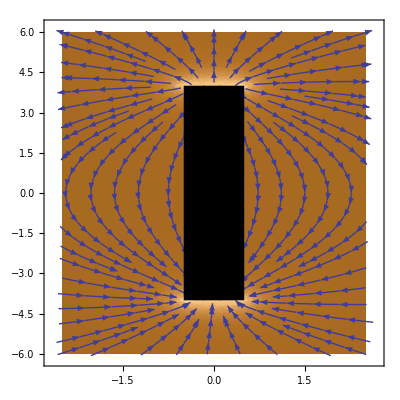

```mathematica
Show[StreamDensityPlot[Hplot[x,z][[{1,3}]],{x,z}∈bar],Graphics[barMagnet]]
```